```mathematica
ClearAll;
y[n_]:=UnitStep[n]-UnitStep[n-5];
```

```mathematica
x[n_]:=y[n/2]+2y[n/2-1/2];
```

```mathematica
yd[n_]:=If[IntegerQ[n],UnitStep[n]-UnitStep[n-5],0]
xd[n_]:=yd[n/2]+2yd[n/2-1/2];
```

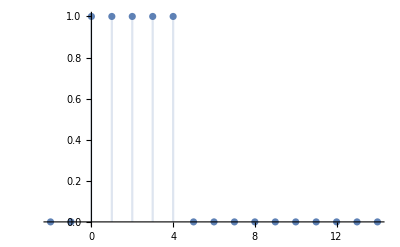

```mathematica
DiscretePlot[yd[n],{n,-2,14}]
```

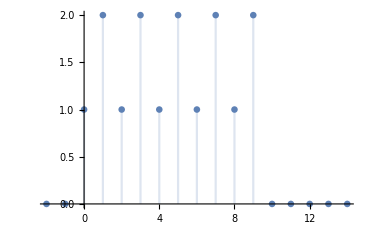

```mathematica
DiscretePlot[xd[n],{n,-2,14}]
```

```mathematica
DFT[xx_,n_,ω_]:=∑_(n=-1)^10 xx[n]*ⅇ^(-I ω n)
```

```mathematica
DFT[yd,n,ω]
```

1+ⅇ^(-ⅈ ω)+ⅇ^(-2 ⅈ ω)+ⅇ^(-3 ⅈ ω)+ⅇ^(-4 ⅈ ω)